```mathematica
(*ClearAll["Global`*"]*)
(*This is a Mathematica program to calculate the band structure of Si using the Empirical Pseudopotential Method.It is based on the work of Chelikowsky et al.,see for example PRB 40,9644 (1989).Atomic units are used everywhere*)(*Lattice*)latticeVec={{0,1/2,1/2},{1/2,0,1/2},{1/2,1/2,0}}   (*fcc lattice*)
reciprocalVec=Transpose[Inverse[latticeVec]]    (*reciprocal lattice/2 pi*)
aLattice=10.26    (*lattice constant for Silicon*)
vAtomic=(1/8) aLattice^3
(*Form factor*)
```

{{0,1/2,1/2},{1/2,0,1/2},{1/2,1/2,0}}

{{-1,1,1},{1,-1,1},{1,1,-1}}

10.26

135.006

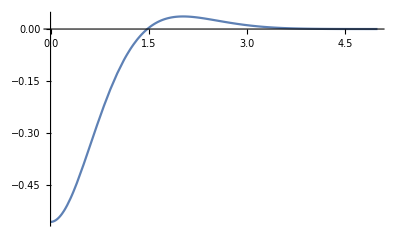

```mathematica
(*Clear[A,Ra,ks,k] siPseudo[k_]:=(-16 Pi+A k^2) Exp[-(k^2*Ra^2)/4]/(k^2+ks^2);
Ra=0.9;ks=0.35;A=16 Pi/1.48^2;*)


(*These parameters were almost obtained by Alvaro Ladeira and Yasser Omar.Ra is a pseudo-potential radius,ks a Thomas-Fermi screaning,A is a normalization*)

siPseudo[k_]:=36.25 (k^2-1.48^2)/(2.06 Exp[(k^2*1.3957^2)/4]-1);

(*These are the parameters of Wang and Zunger,JPC 98,2158 (1994).*)

siPseudoSCLC[k_]:=37.66 (k^2-1.488^2)/(0.2659 Exp[(k^2*1.858^2)/4]+1);

(*These are the parameters of Schluter,Chelikowsky,Louie and Cohen,PRB 12,4200 (1975).*)

Plot[siPseudo[x]/vAtomic,{x,0,5}]    (*plots the form factor*)
```

```mathematica
(*G-space construction*)

nsize=3;(*increase it as needed*)indicesTri=Flatten[Outer[List,Table[i,{i,-nsize,nsize}],Table[i,{i,-nsize,nsize}],Table[i,{i,-nsize,nsize}]],2];
gspaceVec=indicesTri.reciprocalVec;

(*Run this section with a small value of nsize and without the semi-colon to see what Mathematica is doing*)

(*Plane-wave hamiltonian construction*)

emax=4.0;
qlim=2.5;
qincr=0.01
For[q=0,q<qlim,q=q+qincr,
(*Energy cut-off*)kVec={q,0.0,0.0};(*point Gamma in Brillouin zone*)kplusgVec=Table[kVec,{i,Dimensions[gspaceVec][[1]]}]+N[gspaceVec];
kplusgVecOrdered=Sort[kplusgVec,(#1.#1<#2.#2)&];
kplusgVecSelected=Select[kplusgVecOrdered,((1/2)*(N[2Pi]/aLattice)^2*#.#<emax)&];

matSize=Dimensions[kplusgVecSelected][[1]]  ;  (*hamiltonian size*)
kineticOperator=DiagonalMatrix[Table[(1/2)*(N[2Pi]/aLattice)^2*(kplusgVecSelected[[i]].kplusgVecSelected[[i]]),{i,Dimensions[kplusgVecSelected][[1]]}]];
localOperator=Table[(1/vAtomic)*siPseudo[(2 Pi/aLattice)*Sqrt[(kplusgVecSelected[[i,1]]-kplusgVecSelected[[j,1]])^2+(kplusgVecSelected[[i,2]]-kplusgVecSelected[[j,2]])^2+(kplusgVecSelected[[i,3]]-kplusgVecSelected[[j,3]])^2]]*Cos[2N[Pi](kplusgVecSelected[[i,1]]-kplusgVecSelected[[j,1]]+kplusgVecSelected[[i,2]]-kplusgVecSelected[[j,2]]+kplusgVecSelected[[i,3]]-kplusgVecSelected[[j,3]])/8],{i,Dimensions[kplusgVecSelected][[1]]},{j,Dimensions[kplusgVecSelected][[1]]}];

(*The structure factor is the cosine function*)

(*Diagonalization*)

nBand=8;(*Number of bands we want*)
Energias=Take[Sort[Eigenvalues[kineticOperator+localOperator]],nBand];

If[q==0,LEnergias4={Part[Energias,4]*27.212};LEnergias5={Part[Energias,5]*27.12}];
LEnergias4=Join[LEnergias4,{Part[Energias,4]*27.212}];
LEnergias5=Join[LEnergias5,{Part[Energias,5]*27.212}]]

(*Choose another point and recalculate*)
```

0.01

### 5.2a)

```mathematica
(*Hiato Directo no ponto k⃗=(0,0,0)*) 
(Part[LEnergias5,1]-Part[LEnergias4,1])
```

3.32354

### 5.2 b )

```mathematica
(*5.2*)
(*Hiato indirecto em eV, o modelo bate de acordo com o hiato do silício*)
```

```mathematica
Min[LEnergias5]- Max[LEnergias4]
```

1.1051

### Gráfico da banda de valência e banda de condução

```mathematica
E4=ListPlot[Table[{{q,Part[LEnergias4,(q/qincr+1)]}},{q,0,qlim-qincr,qincr}],PlotStyle->Red,PlotLegends->Placed[PointLegend[{Red},{"Banda de Valência"}],{Right,Bottom}]];
E5=ListPlot[Table[{{q,Part[LEnergias5,(q/qincr+1)]}},{q,0,qlim-qincr,qincr}],PlotStyle->Green,PlotLegends->Placed[PointLegend[{Green},{"Banda de Condução"}],{Right,Bottom}]]; 
Pt1=Graphics[{Yellow,PointSize[0.02],Point[{2.02,Part[LEnergias4,203]}]}];
Pt2=Graphics[{Yellow,PointSize[0.02],Point[{1.16,Part[LEnergias5,117]}]}];
linha1=Graphics[{Blue,Line[{{2.02,Part[LEnergias4,203]},{2.02,Part[LEnergias5,117]}}]}];
linha2=Graphics[{Blue,Line[{{2.02-0.02,Part[LEnergias4,203]},{2.02+0.02,Part[LEnergias4,203]}}]}];
linha3=Graphics[{Blue,Line[{{2.02-0.02,Part[LEnergias5,117]},{2.02+0.02,Part[LEnergias5,117]}}]}];
label1=Graphics[Rotate[Text[Style["ΔE",FontSize->10],{2.02+0.1,-4.5}],90 Degree]];
```

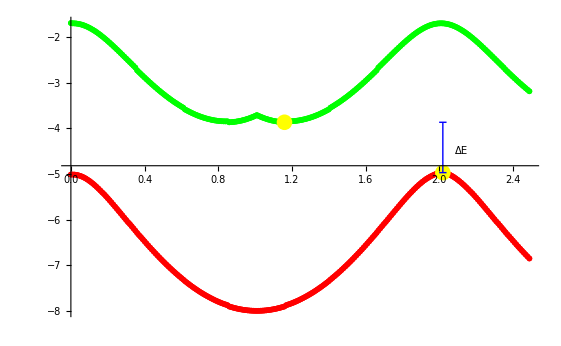

```mathematica
Show[E4,E5,Pt1,Pt2,linha1,linha2,linha3,label1, PlotRange->All]
```